# e.Numeric.series-full.rencon2.strange.L-1.00.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.sea-valence\e.Numeric.series-full.rencon2.strange.L-1.00.nb

## note

use full integral analytic expression to draw pictures.

s flavor in proton has no contribution, so  the rencon is zero.

for perspective quark, use perspective fucoeandmrrlnm

this nb is to numeric evaluating the Γμs

and draw pictures.

if consider 1/((1+Q^2/Λ^2)^2)→c^2/((1+Q^2/Λ^2)^2) ,c^2=((Λ^2+mπ^2)/Λ^2)^2,then c^2={1.05349 mπ, 1.79549 mKi, 2.0984 mη}

for different particles, use different rencon

## Initial

inital by hand

```mathematica
<<X`
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
choplimit=10^-8;
```

## coefficients & mass constants

a 4 component list, contain all, u,d,s

coe list and mass rule list initial

```mathematica
Once[fucoe=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

```mathematica
Once[fumass=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

coe list and mass rule get

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"analytic-storage.strange.series-full"}]]
```

```mathematica
zero`directory=FileNameJoin[{NotebookDirectory[],"analytic-storage.strange.series-o0"}]
```

```mathematica
coe`directory=FileNameJoin[{NotebookDirectory[],"expression-coes"}]
```

```mathematica
fucoeandmrrlnm={
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.all.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.u.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.d.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.s.m"}]
};
```

```mathematica
Once[chpt`qfb`quench`coemass=Get[FileNameJoin[{coe`directory,"chpt`qfb`quench`coemass.m"}]]];
Once[chpt`qfa`sea`coemass=Get[FileNameJoin[{coe`directory,"chpt`qfa`sea`coemass.m"}]]];
Once[chpt`qfa`valence`coemass=Get[FileNameJoin[{coe`directory,"chpt`qfa`valence`coemass.m"}]]];
```

```mathematica
Once[
fucoeandmrrlraw=Map[Get,fucoeandmrrlnm,1]
];
```

```mathematica
Once[
fucoeandmrrl=Join[fucoeandmrrlraw,
Transpose[chpt`qfb`quench`coemass,{2,3,1}],
Transpose[chpt`qfa`valence`coemass,{2,3,1}],
Transpose[chpt`qfa`sea`coemass,{2,3,1}]
]
];
```

```mathematica
fucoeandmrrlraw//Dimensions
fucoeandmrrl//Dimensions
```

{13,11,8}

mass constant

## order

conmo={1Σ,2Neu,3Ξ,4Λ}--{1Σm,2Σ0,3Σp,4pr,5ne,6Ξm,7Ξ0,8Λ}

conmm={1π,2Ki,3η},

conmd={1Δ,2Σs,3Ξs,4Ω}

## assign value

```mathematica
Once[
{conmπ,conmKi,conmη,conmEtas}={
0.1381,
0.4956,
0.5693,
0.9452
}
];
```

```mathematica
Once[
{conmΣ,conmN,conmΞ,conmΛ,conmΛΣ,
conmUUU,conmDDD,conmSSS(* the symmetric terms *)
}={
1.193,0.939,1.315,1.116,1.155,
0.939,0.939,1.315
}
];
```

```mathematica
{conmΔ,conmΣs,conmΞs,conmΩ}={
1.232,
1.385,
1.530,
1.672
};
```

```mathematica
{conmN,conmη,conmΞs}
```

{0.939,0.5693,1.53}

fu Coefficients mass rules reduce

## fu Coefficients

in {4,9} external sign[-]

fusign8,fusign9

```mathematica
fucoepresign={
(*+++++++++++++++++++111++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,fusign8,(*8*)fusign9,(*9*)
1,1(*11*)},
(*+++++++++++++++++++222++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)},
(*+++++++++++++++++++333++++++++++++++++++++++++++++++++++++++*)
{1,1,1,(*3*)
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)}(*fch's sign*)
}⟦3⟧;
```

1 for fitting, 2 for calc/test,

```mathematica
(*fucoeandmrrlraw [consti,figure,octet][4*11*8]*)
fucoe=Table[
Simplify[
fucoepresign*Values[fucoeandmrrl⟦i⟧]
]
,{i,1,13,1}
];//AbsoluteTiming
```

{2.07589,Null}

## fu mass rules

```mathematica
fumass=Keys[fucoeandmrrl];
```

```mathematica
fucoe//Dimensions
fumass//Dimensions
```

{13,11,8}

{13,11,8}

magnetic momentum tree level

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613};

rule lists

```mathematica
constmo={
(*1*)conmΣ,(*2*)conmΣ,(*3*)conmΣ,
(*4*)conmN,(*5*)conmN,
(*6*)conmΞ,(*7*)conmΞ,
(*8*)conmΛ
};
```

```mathematica
baselist1={
{mN->conmΣ},{mN->conmΣ},{mN->conmΣ},
{mN->conmN},{mN->conmN},
{mN->conmΞ},{mN->conmΞ},
{mN->conmΛ}
};
```

c1→2.081,c2→(2/3 c1-1),c3→(-1/3 c1-1)

```mathematica
c3 = c2 - c1;
```

```mathematica
baselist2={
f->0.093,
zi->-1,
di->0.76,fi->0.50,
ci->1,Λ0->1,
c1->1.989685684566755,c2->0.7340985660824763
};
```

for neutron pull-apart, best octet fit Λ0≈1~0.1

```mathematica
baselist=Table[
Join[baselist1⟦i⟧,baselist2]
,{i,1,8,1}
];
```

## para-c1c2.sum-square.all-baryons.rencon2

*********************************************************************

ci→1,Λ0→0.7,
{0.140654,{c1→2.01272,c2→0.477586}}

ci→1,Λ0→0.75,
{0.132188,{c1→1.95069,c2→0.441996}}

ci→1,Λ0→0.8,
{0.126797,{c1→1.88383,c2→0.405126}}

ci→1,Λ0→0.85,
{0.123918,{c1→1.81213,c2→0.36732}}

ci→1,Λ0→0.90,
{0.123053,{c1→1.73562,c2→0.329194}}

ci→1,Λ0→0.95,
{0.123788,{c1→1.65425,c2→0.291768}}

ci→1,Λ0→1.0,
{0.125804,{c1→1.56783,c2→0.256696}}

ci→1,Λ0→1.05,
{0.128887,{c1→1.4758,c2→0.226666}}

ci→1,Λ0→1.1,
{0.132961,{c1→1.37675,c2→0.206175}}

**********************************************************************************

ci→1,Λ0→0.90,
{0.123053,{c1→1.73562,c2→0.329194}}

Λ0→0.90,ci→1.05,
{0.114994,{c1→1.69533,c2→0.331066}}

Λ0→0.90,ci→1.1,
{0.107251,{c1→1.65427,c2→0.334366}}

Λ0→0.90,ci→1.15,
{0.099849,{c1→1.61237,c2→0.339155}}

Λ0→0.90,ci→1.2,

{0.0928122,{c1→1.56956,c2→0.345494}}

Λ0→0.90,ci→1.25,
{0.0861669,{c1→1.52573,c2→0.353452}}

Λ0→0.90,ci→1.3,
{0.0799395,{c1→1.48082,c2→0.363103}}

Λ0→0.90,ci→1.35,

{0.0741573,{c1→1.43471,c2→0.374525}}

Λ0→0.90,ci→1.40,
{0.0688482,{c1→1.38729,c2→0.387806}}

Λ0→0.90,ci→1.45,
{0.0640414,{c1→1.33846,c2→0.403039}}

Λ0→0.90,ci→1.5,
{0.0597673,{c1→1.28808,c2→0.420326}}

*************************************************************************

Λ0→0.80,ci→1,
{0.126797,{c1→1.88383,c2→0.405126}}

Λ0→0.80,ci→1.05,
{0.119196,{c1→1.85488,c2→0.403562}}

Λ0→0.80,ci→1.1,
{0.111782,{c1→1.82541,c2→0.402675}}

Λ0→0.80,ci→1.15,
{0.104581,{c1→1.79539,c2→0.402487}}

Λ0→0.80,ci→1.2,

{0.097619,{c1→1.7648,c2→0.403024}}

Λ0→0.80,ci→1.25,
{0.0909201,{c1→1.73361,c2→0.40431}}

Λ0→0.80,ci→1.3,
{0.0845108,{c1→1.70178,c2→0.406373}}

Λ0→0.80,ci→1.35,

{0.0784171,{c1→1.6693,c2→0.409241}}

Λ0→0.80,ci→1.40,
{0.0726658,{c1→1.63611,c2→0.412944}}

Λ0→0.80,ci→1.45,
{0.0672835,{c1→1.60219,c2→0.417514}}

Λ0→0.80,ci→1.5,
{0.0622978,{c1→1.56749,c2→0.422984}}

************************************************************

Λ0→0.85,ci→1.5,
{0.0597742,{c1→1.43562,c2→0.412794}}

Λ0→1,ci→1.5,
{0.0654518,{c1→0.917221,c2→0.539694}}

## para test c1c2 sum - square

fch,ci→1,Λ0→0.9,
c1→2.081,c2→0.788,c3→-1.693
{0.0434328,{c1→2.00193}}

ci→1,Λ0→0.8,
 {4.55972×10^-17,{c1→2.14188,c2→0.756261}}

ci→1,Λ0→0.85,
 {6.40949×10^-31,{c1→2.09749,c2→0.752286}}

ci→1,Λ0→0.90,
 {1.33761×10^-17,{c1→2.05739,c2→0.747545}}

ci→1,Λ0→0.95
 {3.9443×10^-31,{c1→2.02149,c2→0.741624}}

ci→1,Λ0→1.0,
 {1.32802×10^-16,{c1→1.98969,c2→0.734099}}

## Γμ get

pure diagram form-factor

```mathematica
Clear[ff1,ff2]
```

```mathematica
Once[Monitor[
ff1=Table[
Get[
FileNameJoin[{Directory[],"f1."<>"analytic."<>ToString[i]<>".m"}]
]
,{i,1,11,1}];
ff2=Table[
Get[
FileNameJoin[{Directory[],"f2."<>"analytic."<>ToString[j]<>".m"}]
]
,{j,1,11,1}];
,{i,j}]//AbsoluteTiming]
```

{33.0701,Null}

```mathematica
Once[Monitor[
zero`ff1=Table[
Get[
FileNameJoin[{zero`directory,"f1."<>"analytic."<>ToString[i]<>".m"}]
]
,{i,1,11,1}];
zero`ff2=Table[
Get[
FileNameJoin[{zero`directory,"f2."<>"analytic."<>ToString[j]<>".m"}]
]
,{j,1,11,1}];
,{i,j}]//AbsoluteTiming]
```

{0.21955,Null}

```mathematica
ff1//Dimensions
zero`ff2//Dimensions
```

{11}

{11}

form-factor f1, f2

## form-factor list

fucoe=11[diagram]*8[octet]*n(a coefficients lists of n elements)

fumass=11[diagram]*8[octet]*n(n ==above n,n mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

```mathematica
fucoe[[2,4]]
```

```mathematica
Length[fucoe[[2,4]]]
```

contribution combine coefficients,f1, f2

```mathematica
SetOptions[Simplify,TimeConstraint->1];
```

fucoe=11[diagram]*8[octet]*n(coefficients)

fumass=11[diagram]*8[octet]*n(n =above n,mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

```mathematica
Once[nuff1=Table[0,{consti,1,13,1}]];
Once[nuff2=Table[0,{consti,1,13,1}]];
```

```mathematica
Monitor[
Table[
(nuff1⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff1⟦diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
(nuff2⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff2⟦diag⟧
)/.baselist⟦oct⟧/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
,{constituent,1,13,1}
];
,{constituent,oct,diag,coe}
]//AbsoluteTiming
```

{7963.36,Null}

```mathematica
(*nuff1,nuff2 is 4*8*)
nugegm=Transpose[(*8*4*2 transpose into 4*8*2*)
Table[
-1/(16 π^2){
nuff1⟦;;,i⟧-Q2/(4 constmo⟦i⟧^2)nuff2⟦;;,i⟧,
nuff1⟦;;,i⟧+nuff2⟦;;,i⟧
}
,{i,1,8,1}]
,{2,3,1}
];//AbsoluteTiming
```

{0.0115861,Null}

```mathematica
nuff1//Dimensions
nuff2//Dimensions
nugegm//Dimensions
```

{4,8}

{4,8}

{4,8,2}

## zero`nuff1 zero`nuff2

```mathematica
zero`nuff1=Table[0,{consti,1,13,1}];
zero`nuff2=Table[0,{consti,1,13,1}];
```

```mathematica
Monitor[
Table[
(
zero`nuff1⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*zero`ff1⟦diag⟧
)/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]);
(
zero`nuff2⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*zero`ff2⟦diag⟧
)/.baselist⟦oct⟧/.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{2,3}]
);
,{constituent,1,13,1}
];
,{constituent,oct,diag,coe}
]//AbsoluteTiming
(*nuff1,nuff2 is 4*8*)
```

{74.9963,Null}

```mathematica
zero`nugegm=Transpose[(*8*4*2 transpose into 4*8*2*)
Table[
-1/(16 π^2){
zero`nuff1⟦;;,i⟧-Q2/(4 constmo⟦i⟧^2)zero`nuff2⟦;;,i⟧,
zero`nuff1⟦;;,i⟧+zero`nuff2⟦;;,i⟧
}
,{i,1,8,1}]
,{2,3,1}
];//AbsoluteTiming
```

{0.0048802,Null}

```mathematica
zero`nuff1//Dimensions
zero`nuff2//Dimensions
zero`nugegm//Dimensions
```

{13,8}

{13,8}

{13,8,2}

## tree level contributions

initial

because history reasons, all mass mo here is marked as mN

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(c1 Q2)/(√3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(4 c1 mN^2)/(√3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

```mathematica
trf1f2={
(*+++++++++++++++++total++++++++++++++++++++++++*)
{{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{-(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}},
(*+++++++++++++++++u++++++++++++++++++++++++*)
{
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++d++++++++++++++++++++++++*)
{
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++s++++++++++++++++++++++++*)
{{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+4 c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (4 c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}}
}/.mo->mN;
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

gegm

-I el(4 mN^2+c1 Q2)/(4 mN^2+Q2) ,--el/(2mN)(4 (c1-1) mN^2)/(4 mN^2+Q2)

netrf1f2⟦4⟧={(4 mN^2+c1 Q2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2),(4 (c1-1) mN^2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2)}/.baselist

```mathematica
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

```mathematica
trgegm=Transpose[
Table[
Simplify[
{
trf1f2⟦;;,i,1⟧-Q2/(4 constmo⟦i⟧^2)trf1f2⟦;;,i,2⟧,
trf1f2⟦;;,i,1⟧+trf1f2⟦;;,i,2⟧
}/.baselist⟦i⟧
]
,{i,1,8,1}]
,{2,3,1}];//AbsoluteTiming
(*trgegm is [consti,octet,treegegem][4*8*2]*)
```

{0.021016,Null}

```mathematica
trgegm//Dimensions
```

{4,8,2}

plot

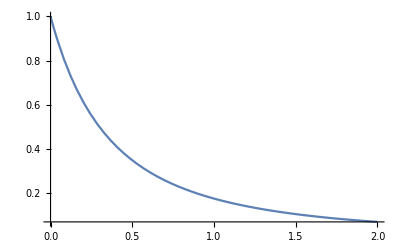

```mathematica
Plot[
trgegm⟦4,1⟧
,{Q2,0.,2.},PlotRange->Full
]
```

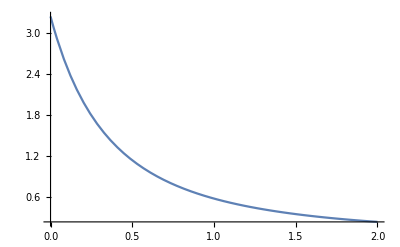

```mathematica
Plot[
trgegm⟦4,2⟧
,{Q2,0.,2.},PlotRange->Full
]
```

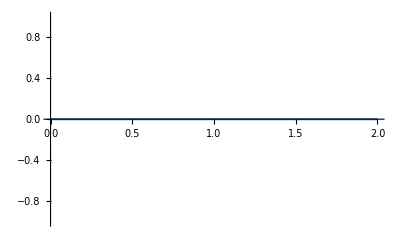

```mathematica
Plot[
trgegm⟦5,1⟧
,{Q2,0.,2.},PlotRange->Full]
```

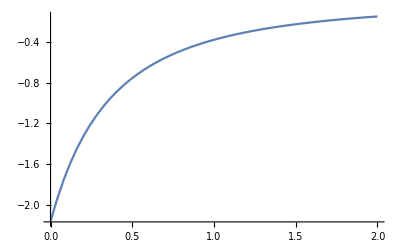

```mathematica
Plot[
trgegm⟦5,2⟧
,{Q2,0.,2.},PlotRange->Full]
```

## loopd0

```mathematica
octetname=
{"1Σm","2Σ0","3Σp","4pr","5ne" ,"6Ξm","7Ξ0","8Λ"};
```

loop derivative coefficient

to order 0

{loopged0,loopgmd0}

nugegm⟦consti,oct,F1F2⟧4*8*2

```mathematica
{loopged0,loopgmd0}=Transpose[(*[oct,loop,consti]8*6*4 transpose into [loop,consti,oct][6*4*8]*)
Table[
{
zero`nugegm⟦;;,oct,1⟧,
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
zero`nugegm⟦;;,oct,2⟧
}
,{oct,1,8,1}
]
,{3,1,2}];//AbsoluteTiming
(*{loopged0,loopgmd0} ⟦consti,oct⟧[4,8]*)
```

{0.0005189,Null}

```mathematica
loopged0//Dimensions
loopgmd0//Dimensions
```

{13,8}

{13,8}

## rencon calc

constants

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

```mathematica
octetcharge={
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
};
```

```mathematica
octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613};
```

rencon2.13

```mathematica
rencon=Table[1,{seva,1,13,1},{io,1,8,1}];
(*+++++++++++++++++renormalized according to charge+++++++++++++*)
Table[
rencon⟦;;,i⟧=Abs[octetcharge⟦i⟧-Re[(Cancel[Chop[loopged0⟦1,i⟧,choplimit]]/.Q2->0)]]
,{i,{1,3,4,6}}];
rencon⟦;;,2⟧=rencon⟦;;,3⟧;
rencon⟦;;,5⟧=rencon⟦;;,4⟧;
rencon⟦;;,7⟧=rencon⟦;;,6⟧;
rencon⟦;;,8⟧=Abs[1-Re[(Cancel[Chop[loopged0⟦2,8⟧,choplimit]]/.Q2->0)]];
(*++++++++++++++++++++no renormalized+++++++++++++++++++++*)
(*rencon⟦2,1⟧=1;
rencon⟦2,6⟧=1;
rencon⟦3,3⟧=1;
rencon⟦3,7⟧=1;
rencon⟦4,4⟧=1;
rencon⟦4,5⟧=1;*)
(*++++++++++++++++++++display+++++++++++++++++++++*)
TableForm[rencon,TableHeadings->{Automatic,None}]
```

1 | 0.708159 | 0.708159 | 0.708159 | 0.646099 | 0.646099 | 0.822521 | 0.822521 | 0.750395
2 | 0.708159 | 0.708159 | 0.708159 | 0.646099 | 0.646099 | 0.822521 | 0.822521 | 0.750395
3 | 0.708159 | 0.708159 | 0.708159 | 0.646099 | 0.646099 | 0.822521 | 0.822521 | 0.750395
4 | 0.708159 | 0.708159 | 0.708159 | 0.646099 | 0.646099 | 0.822521 | 0.822521 | 0.750395

## Q2 table

Q2  table initial

```mathematica
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
(*trgegm is [consti,octet,treegegem][4*8*2]*)
```

```mathematica
octetcharge={
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
};
```

```mathematica
octetmageton={
(*1*)−1.160,(*2*)0.60,(*3*)2.458,
(*4*)2.7928473446,(*5*)−1.9130427,
(*6*)−0.6507,(*7*)−1.250,
(*8*)−0.613
};
```

```mathematica
octet`ge`gem={
{
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
},
{
(*1*)−1.160,(*2*)0.60,(*3*)2.458,
(*4*)2.7928473446,(*5*)−1.9130427,
(*6*)−0.6507,(*7*)−1.250,
(*8*)−0.613
}
};
```

```mathematica
getree=Re[trgegm⟦;;,;;,1⟧/.Q2->0];
```

```mathematica
gmtree=Re[trgegm⟦;;,;;,2⟧/.Q2->0];
```

```mathematica
gegmtree=Re[trgegm/.Q2->0];
```

```mathematica
octetnameabbr=
{"Σm","Σ0","Σp","pr","ne","Ξm","Ξ0","Λ"};
```

```mathematica
term`name={"tree","loop","tot","exp.","diff","per","u","d","s"};
```

```mathematica
(*getree is [consti,octet,][4*8]*)
(*gmtree is [consti,octet,][4*8]*)
(*gegmtree is [consti,octet,treegegem][4*8*2]*)
```

```mathematica
geconstiname={"Ge.all","Ge.u","Ge.d","Ge.s"};
gmconstiname={"Gm.all","Gm.u","Gm.d","Gm.s"};
```

ge & gm

```mathematica
(*nugegm is [consti,octet,treegegem][4*8*2]i.e. loopge0 loopgm0*)
(*{cur2ereci,cur2mreci} are ⟦consti,oct⟧[4,8]*)
```

```mathematica
Column[
Table[
Column[
(*+++++++++++++++++++++++++++++++++++++++ total start +++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
{
tetable=Re[
Cancel[Chop[({loopged0,loopgmd0}⟦gegmord⟧),choplimit]]/.Q2->0
];
Labeled[
TableForm[
(*add "tot.","gmexpect","diff"*)
(*gegmtree [consti,octet,gegm]*)
(*tetable [consti,octet]*)
(*rencon [consti,octet]*)
{
Chop[rencon⟦1⟧*gegmtree⟦1,;;,gegmord⟧,choplimit],
Chop[rencon⟦1⟧*tetable⟦1⟧,choplimit],
Chop[rencon⟦1⟧*(gegmtree⟦1,;;,gegmord⟧+tetable⟦1⟧),choplimit],
Chop[octet`ge`gem⟦gegmord⟧,choplimit],(*octet charge and mageton exprimental*)
Chop[octet`ge`gem⟦gegmord⟧-rencon⟦1⟧*(gegmtree⟦1,;;,gegmord⟧+tetable⟦1⟧),choplimit],
If[gegmord==2,
(ToString[#,TraditionalForm]<>"%")&/@

(((octet`ge`gem⟦gegmord⟧-rencon⟦1⟧*(gegmtree⟦1,;;,gegmord⟧+tetable⟦1⟧))/octet`ge`gem⟦gegmord⟧)*100),Nothing(*false for ge gegmord==1*)
]
}
(*formatting*)
,TableHeadings->{
term`name,
octetnameabbr
},
TableSpacing->{2, 2}
]
,{"Ge.tot.","Gm.tot."}⟦gegmord⟧
,{{Top,Left}}
,LabelStyle->Directive[Red,Bold,20,FontFamily->"Times New Roman"]
],
(*+++++++++++++++++++++++++++++++++++++++ flavor start +++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Labeled[
TableForm[
(*add "tot.","gmexpect","diff"*)
{
(*++++++++++++++++++++ tree ++++++*)
Chop[rencon⟦2⟧*gegmtree⟦2,;;,gegmord⟧,choplimit],
Chop[rencon⟦3⟧*gegmtree⟦3,;;,gegmord⟧,choplimit],
Chop[rencon⟦4⟧*gegmtree⟦4,;;,gegmord⟧,choplimit],
(*++++++++++++++++++++ loop ++++++*)
Chop[rencon⟦2⟧*tetable⟦2⟧,choplimit],
Chop[rencon⟦3⟧*tetable⟦3⟧,choplimit],
Chop[rencon⟦4⟧*tetable⟦4⟧,choplimit],
(*++++++++++++++++++++ total ++++++*)
Chop[rencon⟦2⟧*(gegmtree⟦2,;;,gegmord⟧+tetable⟦2⟧),choplimit],
Chop[rencon⟦3⟧*(gegmtree⟦3,;;,gegmord⟧+tetable⟦3⟧),choplimit],
Chop[rencon⟦4⟧*(gegmtree⟦4,;;,gegmord⟧+tetable⟦4⟧),choplimit]
}
(*formatting*)
,TableHeadings->{
{
"u-tree","d-tree","s-tree",
"u-loop","d-loop","s-loop",
"u-tot.","d-tot.","s-tot."
},
octetnameabbr
},
TableSpacing->{2.5, 3}
],
({"Ge.consti.","Gm.consti."}⟦gegmord⟧),
{{Top,Left}},
LabelStyle->Directive[Red,Bold,20,FontFamily->"Times New Roman"]
]
}
,Spacings->1.5],
(* gegmord ge1, gm2*)
{gegmord,1,2,1}
]
,Dividers->{None,{1->Blue,2->Blue,3->Blue}}
,Spacings->4
]
```

| Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.714292 | 0 | 0.714292 | 0.680134 | 0 | -0.786641 | 0 | 0
loop | -0.285708 | 0 | 0.285708 | 0.319866 | 0 | -0.213359 | 0 | 0
tot | -1. | 0 | 1. | 1. | 0 | -1. | 0 | 0
exp. | -1 | 0 | 1 | 1 | 0 | -1 | 0 | 0
diff | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0Ge.tot.
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
u-tree | 0 | 0.714292 | 1.42858 | 1.36027 | 0.680134 | 0 | 0.786641 | 0.737229
d-tree | 1.42858 | 0.714292 | 0 | 0.680134 | 1.36027 | 0.786641 | 0 | 0.737229
s-tree | 0.714292 | 0.714292 | 0.714292 | 0 | 0 | 1.57328 | 1.57328 | 0.737229
u-loop | 0 | 0.285708 | 0.571416 | 0.639731 | 0.319866 | 0 | 0.213359 | 0.262771
d-loop | 0.571416 | 0.285708 | 0 | 0.319866 | 0.639731 | 0.213359 | 0 | 0.262771
s-loop | 0.285708 | 0.285708 | 0.285708 | 0 | 0 | 0.426718 | 0.426718 | 0.262771
u-tot. | 0 | 1. | 2. | 2. | 1. | 0 | 1. | 1.
d-tot. | 2. | 1. | 0 | 1. | 2. | 1. | 0 | 1.
s-tot. | 1. | 1. | 1. | 0 | 0 | 2. | 2. | 1.Ge.consti.
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.758399 | 0.489858 | 1.73811 | 1.655 | -0.932866 | -0.835216 | -1.07895 | -0.505588
loop | -0.615007 | 0.207615 | 1.03024 | 1.13785 | -0.980177 | -0.183065 | -0.517463 | -0.253543
tot | -1.37341 | 0.697473 | 2.76835 | 2.79285 | -1.91304 | -1.01828 | -1.59641 | -0.759131
exp. | -1.16 | 0.6 | 2.458 | 2.79285 | -1.91304 | -0.6507 | -1.25 | -0.613
diff | 0.213406 | -0.0974726 | -0.310351 | 0 | 0 | 0.367581 | 0.346413 | 0.146131
per | -18.3971% | -16.2454% | -12.6262% | 1.28477×10^-7% | -3.70022×10^-8% | -56.4901% | -27.713% | -23.8387%Gm.tot.
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
u-tree | -0.375955 | 0.979716 | 2.22797 | 2.12143 | -0.466433 | -0.375955 | -0.539475 | 0
d-tree | 2.22797 | 0.979716 | -0.375955 | -0.466433 | 2.12143 | -0.539475 | -0.375955 | 0
s-tree | -0.489858 | -0.489858 | -0.489858 | -0.375955 | -0.375955 | 2.45364 | 2.45364 | 1.51676
u-loop | -0.66073 | 0.350668 | 1.17329 | 1.30618 | -0.811843 | -0.079357 | -0.396824 | -0.105479
d-loop | 1.17329 | 0.350668 | -0.66073 | -0.811843 | 1.30618 | -0.396824 | -0.079357 | -0.105479
s-loop | -0.272177 | -0.272177 | -0.272177 | 0.0156769 | 0.0156769 | 0.821167 | 0.821167 | 0.655151
u-tot. | -1.03668 | 1.33038 | 3.40126 | 3.42761 | -1.27828 | -0.455312 | -0.936299 | -0.105479
d-tot. | 3.40126 | 1.33038 | -1.03668 | -1.27828 | 3.42761 | -0.936299 | -0.455312 | -0.105479
s-tot. | -0.762034 | -0.762034 | -0.762034 | -0.360278 | -0.360278 | 3.27481 | 3.27481 | 2.17191Gm.consti.

consistency test

```mathematica
octetmageton`c1c2c3={
(*1 Σ*)-1+1/3 (c1-3 c2),c1/3,1+1/3 (c1+3 c2),
(*4 N*)1+1/3 (c1+3 c2),-(2 c1)/3,
(*6 Ξ*)-1+1/3 (c1-3 c2),-(2 c1)/3,
(*4 Λ*)-c1/3
};(*described by μu && μs (substitute with c1 c2 c3)*)
rencon*gmtree⟦1⟧
rencon*octetmageton`c1c2c3/.baselist2
```

{-0.806835,0.552668,1.91217,1.82452,-1.05467,-0.885198,-1.21269,-0.571348}

{-0.806835,0.552668,1.91217,1.82452,-1.05467,-0.885198,-1.21269,-0.571348}

## Q2 table respective

respective f1f2

```mathematica
renuff1=Table[0,{k,1,4,1}];
renuff2=Table[0,{k,1,4,1}];
Monitor[
Table[
(renuff1⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff1⟦diag⟧
)//.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{3}]);
(renuff2⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff2⟦diag⟧
)//.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{3}]);
,{constituent,1,4,1}
];
,{constituent,oct,diag,coe}
]//AbsoluteTiming
(*combine ge gm from f1 f2 *)
(* nuff1,nuff2 is 4*8*11 *)
renugegm=Transpose[(* 8*2*4*11 transpose into 4*11*8*2 *)
Table[
-1/(16 π^2)*{
renuff1⟦;;,i,;;⟧-Q2/(4 constmo⟦i⟧^2)renuff2⟦;;,i,;;⟧,
renuff1⟦;;,i,;;⟧+renuff2⟦;;,i,;;⟧
}
,{i,1,8,1}]
,{3,4,1,2}
];//AbsoluteTiming
```

{17.1432,Null}

{0.0051414,Null}

```mathematica
renugegm//Dimensions
```

{4,11,8,2}

Q2  table.ed2

```mathematica
diagname2={"tree","1a","2b","3c","4de","5fg","6h","7i","8j","9kl","10mn","11op","tot.","diff","diff"};
constiname={"1all","2u","3d","4s"};
```

```mathematica
reconpersdiag=(Nest[Append[#,rencon]&,{rencon},10]);
reconpersdiag//Dimensions
```

{11,8}

## ge

```mathematica
(* renugegm [consti,diagram,oct,f1f2]{4,11,8,2} *)
```

```mathematica
Column[
Table[
Labeled[
tetable=Table[
Re[Simplify[Chop[renugegm⟦constiord,i,j,1⟧,choplimit]]/.Q2->0]
,{i,1,11,1}
,{j,1,8,1}
];
(*give the sign*)
tetablemod=tetable;
(*formatting, add other things *)
TableForm[
(*  add "tot.","gmexpect","diff" *)
Join[
{rencon⟦1⟧*(getree⟦constiord⟧)},
tetablemod,
{
rencon⟦1⟧*(getree⟦constiord⟧+Total[tetablemod,{1}]),
Round[rencon⟦1⟧*(getree⟦constiord⟧+Total[tetablemod,{1}])]-rencon⟦1⟧*(getree⟦constiord⟧+Total[tetablemod,{1}])
}
]
(*formatting*)
,TableHeadings->{
diagname2,
octetnameabbr
}
]
,Style[constiname⟦constiord⟧,"Section"],{{Top,Left}}
]
,{constiord,1,4,1}
]
,Spacings->1.5
]
```

| Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.714292 | 0. | 0.714292 | 0.680134 | 0. | -0.786641 | 0. | 0.
1a | -0.0638834 | 0.00267854 | 0.0692405 | 0.0694516 | -0.0672511 | -0.0168004 | -0.0185803 | -0.0130277
2b | -0.137189 | -0.019921 | 0.0973468 | 0.119781 | 0.230465 | -0.131784 | 0.0889532 | 0.0587293
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.0561723 | 0.00545548 | 0.0670832 | 0.0625687 | -0.0587327 | -0.0265593 | -0.0356485 | -0.0212974
6h | -0.00421838 | -0.0035484 | -0.00287843 | -0.00477466 | 0.00532704 | -0.00523835 | 0.00447232 | 0.000707294
7i | -0.0618989 | 0.0220602 | 0.106019 | 0.126303 | -0.0343797 | -0.0445966 | -0.0243334 | -0.00629402
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | -0.0120411 | -0.011266 | -0.0104908 | -0.017217 | 0.0210087 | -0.0129589 | 0.0131542 | 0.00397306
11op | -0.00711918 | -0.00724588 | -0.00737257 | -0.0067802 | 0.00804396 | -0.00797391 | 0.00670691 | 0.00161367
tot. | -1. | -2.83146×10^-14 | 1. | 1. | 1.1605×10^-13 | -1. | -7.91083×10^-13 | 1.13517×10^-13
diff | -1.11022×10^-16 | 2.83146×10^-14 | 0. | 0. | -1.1605×10^-13 | 0. | 7.91083×10^-13 | -1.13517×10^-131all
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 0. | 0.714292 | 1.42858 | 1.36027 | 0.680134 | 0. | 0.786641 | 0.737229
1a | -0.0638834 | 0.00267854 | 0.0692405 | 0.0694516 | -0.0672511 | -0.0168004 | -0.0185803 | -0.0130277
2b | 0.177522 | 0.294789 | 0.412057 | 0.492547 | 0.603232 | 0.0686763 | 0.289413 | 0.326265
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.0561723 | 0.00545548 | 0.0670832 | 0.0625687 | -0.0587327 | -0.0265593 | -0.0356485 | -0.0212974
6h | -0.00421838 | -0.0035484 | -0.00287843 | -0.00477466 | 0.00532704 | -0.00523835 | 0.00447232 | 0.000707294
7i | 0.0233787 | 0.107338 | 0.191297 | 0.223834 | 0.0631516 | 0.0261712 | 0.0464344 | 0.0826013
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | -0.0120411 | -0.011266 | -0.0104908 | -0.017217 | 0.0210087 | -0.0129589 | 0.0131542 | 0.00397306
11op | -0.00711918 | -0.00724588 | -0.00737257 | -0.0067802 | 0.00804396 | -0.00797391 | 0.00670691 | 0.00161367
tot. | 6.41704×10^-14 | 1. | 2. | 2. | 1. | -1.30227×10^-13 | 1. | 1.
diff | -6.41704×10^-14 | -9.25926×10^-14 | -1.20792×10^-13 | -3.81917×10^-14 | -1.53655×10^-13 | 1.30227×10^-13 | 9.21374×10^-13 | 1.11022×10^-162u
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 1.42858 | 0.714292 | 0. | 0.680134 | 1.36027 | 0.786641 | 0. | 0.737229
1a | 0.0692405 | 0.00267854 | -0.0638834 | -0.0672511 | 0.0694516 | -0.0185803 | -0.0168004 | -0.0130277
2b | 0.412057 | 0.294789 | 0.177522 | 0.603232 | 0.492547 | 0.289413 | 0.0686763 | 0.326265
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | 0.0810401 | 0.011787 | -0.057466 | -0.104481 | 0.120965 | -0.0347245 | -0.0253165 | -0.0244041
5fg | 0.0670832 | 0.00545548 | -0.0561723 | -0.0587327 | 0.0625687 | -0.0356485 | -0.0265593 | -0.0212974
6h | -0.00287843 | -0.0035484 | -0.00421838 | 0.00532704 | -0.00477466 | 0.00447232 | -0.00523835 | 0.000707294
7i | 0.191297 | 0.107338 | 0.0233787 | 0.0631516 | 0.223834 | 0.0464344 | 0.0261712 | 0.0826013
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | -0.0104908 | -0.011266 | -0.0120411 | 0.0210087 | -0.017217 | 0.0131542 | -0.0129589 | 0.00397306
11op | -0.00737257 | -0.00724588 | -0.00711918 | 0.00804396 | -0.0067802 | 0.00670691 | -0.00797391 | 0.00161367
tot. | 2. | 1. | 6.41704×10^-14 | 1. | 2. | 1. | -1.30227×10^-13 | 1.
diff | -7.54952×10^-15 | -9.25926×10^-14 | -6.41704×10^-14 | -1.53655×10^-13 | -3.81917×10^-14 | 9.21374×10^-13 | 1.30227×10^-13 | 1.11022×10^-163d
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 0.714292 | 0.714292 | 0.714292 | 0. | 0. | 1.57328 | 1.57328 | 0.737229
1a | -0.00535709 | -0.00535709 | -0.00535709 | -0.00220049 | -0.00220049 | 0.0353807 | 0.0353807 | 0.0260554
2b | 0.354553 | 0.354553 | 0.354553 | 0.0225202 | 0.0225202 | 0.24329 | 0.24329 | 0.150077
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | -0.023574 | -0.023574 | -0.023574 | -0.0164837 | -0.0164837 | 0.060041 | 0.060041 | 0.0488083
5fg | -0.010911 | -0.010911 | -0.010911 | -0.00383594 | -0.00383594 | 0.0622078 | 0.0622078 | 0.0425949
6h | 0.00709681 | 0.00709681 | 0.00709681 | -0.000552378 | -0.000552378 | 0.000766021 | 0.000766021 | -0.00141459
7i | 0.0411571 | 0.0411571 | 0.0411571 | 0.00560785 | 0.00560785 | 0.139698 | 0.139698 | 0.101483
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | 0.0225319 | 0.0225319 | 0.0225319 | -0.00379172 | -0.00379172 | -0.000195239 | -0.000195239 | -0.00794611
11op | 0.0144918 | 0.0144918 | 0.0144918 | -0.00126375 | -0.00126375 | 0.001267 | 0.001267 | -0.00322734
tot. | 1. | 1. | 1. | -7.82208×10^-14 | -7.82208×10^-14 | 2. | 2. | 1.
diff | -1.2057×10^-13 | -1.77192×10^-13 | -1.77192×10^-13 | 7.82208×10^-14 | 7.82208×10^-14 | -6.61249×10^-13 | -6.61249×10^-13 | 3.40616×10^-134s

## gm

```mathematica
Column[
Table[
Labeled[
tetable=Table[
Re[Simplify[Chop[renugegm⟦constiord,i,j,2⟧,choplimit]]/.Q2->0]
,{i,1,11,1}
,{j,1,8,1}
];
(*give the sign*)
tetablemod=tetable;
(*formatting, add other things *)
TableForm[
(*  add "tot.","gmexpect","diff" *)
Join[
{rencon⟦1⟧*(gmtree⟦constiord⟧)},
tetablemod,
{
rencon⟦1⟧*(gmtree⟦constiord⟧)+Total[tetablemod,{1}],
Round[rencon⟦1⟧*(gmtree⟦constiord⟧+Total[tetablemod,{1}])]-rencon⟦1⟧*(gmtree⟦constiord⟧+Total[tetablemod,{1}])
}
]
(*formatting*)
,TableHeadings->{
diagname2,
octetnameabbr
}
]
,Style[constiname⟦constiord⟧,"Section"],{{Top,Left}}
]
,{constiord,1,4,1}
]
,Spacings->1.5
]
```

| Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.49548 | 0.49548 | 1.48644 | 1.41536 | -0.943573 | -0.545667 | -1.09133 | -0.511391
1a | -0.367197 | 0.0200876 | 0.407372 | 0.398683 | -0.382041 | -0.0744865 | -0.0587635 | -0.0374738
2b | -0.00628454 | -0.00257824 | 0.00112806 | 0.00908518 | 0.0160236 | -0.00673283 | 0.00508738 | 0.00609903
3c | -0.0853004 | -0.00916843 | 0.0669635 | 0.0817439 | -0.0314628 | -0.0439357 | -0.0210462 | -0.0187096
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.257587 | 0.0370242 | 0.331636 | 0.304423 | -0.274784 | -0.100907 | -0.122183 | -0.0593334
6h | 0.0352964 | 0.0178258 | 0.000355271 | 0.0690866 | -0.0775355 | 0.0558069 | -0.062538 | -0.00978052
7i | -0.0013658 | 0.000548604 | 0.00246301 | -0.00192795 | 0.000701335 | -0.00173262 | -0.0014758 | 0.000231942
8j | -0.0882139 | 0.03351 | 0.155234 | 0.16938 | -0.0465872 | -0.0563002 | -0.0261195 | -0.00861953
9kl | -0.0776795 | 0.129947 | 0.337573 | 0.40521 | -0.395766 | -0.0538522 | -0.229222 | -0.159065
10mn | 0.00401372 | 0.00375532 | 0.00349692 | 0.005739 | -0.0070029 | 0.00431965 | -0.00438473 | -0.00132435
11op | 0.0494552 | 0.0359802 | 0.0225052 | 0.0777167 | -0.0955227 | 0.0679546 | -0.0829415 | -0.020544
tot. | -1.34781 | 0.774199 | 2.89621 | 3.05546 | -2.34203 | -0.780849 | -1.72965 | -0.844314
diff | 0.104292 | 0.305433 | -0.493426 | 0.469149 | -0.105287 | -0.269329 | -0.406544 | -0.2431691all
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 0. | 0.990961 | 1.98192 | 1.88715 | -0.471787 | 0. | -0.545667 | 2.00329×10^-16
1a | -0.367197 | 0.0200876 | 0.407372 | 0.398683 | -0.382041 | -0.0744865 | -0.0587635 | -0.0374738
2b | -0.00411223 | -0.000405928 | 0.00330037 | 0.0393651 | 0.0463034 | 0.00218367 | 0.0140039 | 0.0259816
3c | -0.0491543 | 0.0269776 | 0.10311 | 0.125442 | 0.0122356 | -0.0186891 | 0.00420035 | 0.0145959
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.257587 | 0.0370242 | 0.331636 | 0.304423 | -0.274784 | -0.100907 | -0.122183 | -0.0593334
6h | 0.0352964 | 0.0178258 | 0.000355271 | 0.0690866 | -0.0775355 | 0.0558069 | -0.062538 | -0.00978052
7i | 0.00102862 | 0.00294302 | 0.00485742 | -0.00359326 | -0.000963974 | 0.00214407 | 0.00240088 | 0.0024326
8j | 0.0314227 | 0.153147 | 0.274871 | 0.300657 | 0.08469 | 0.0301829 | 0.0603636 | 0.100431
9kl | -0.0776795 | 0.129947 | 0.337573 | 0.40521 | -0.395766 | -0.0538522 | -0.229222 | -0.159065
10mn | 0.00401372 | 0.00375532 | 0.00349692 | 0.005739 | -0.0070029 | 0.00431965 | -0.00438473 | -0.00132435
11op | 0.0494552 | 0.0359802 | 0.0225052 | 0.0777167 | -0.0955227 | 0.0679546 | -0.0829415 | -0.020544
tot. | -0.691979 | 1.43003 | 3.55204 | 3.73084 | -1.66666 | -0.11066 | -1.05946 | -0.168484
diff | 0.494275 | -0.304584 | -0.103443 | -0.141106 | 0.284458 | 0.0870495 | -0.0501658 | 0.1242112u
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 1.98192 | 0.990961 | 0. | -0.471787 | 1.88715 | -0.545667 | 0. | 2.00329×10^-16
1a | 0.407372 | 0.0200876 | -0.367197 | -0.382041 | 0.398683 | -0.0587635 | -0.0744865 | -0.0374738
2b | 0.00330037 | -0.000405928 | -0.00411223 | 0.0463034 | 0.0393651 | 0.0140039 | 0.00218367 | 0.0259816
3c | 0.10311 | 0.0269776 | -0.0491543 | 0.0122356 | 0.125442 | 0.00420035 | -0.0186891 | 0.0145959
4de | 0.0810401 | 0.011787 | -0.057466 | -0.104481 | 0.120965 | -0.0347245 | -0.0253165 | -0.0244041
5fg | 0.331636 | 0.0370242 | -0.257587 | -0.274784 | 0.304423 | -0.122183 | -0.100907 | -0.0593334
6h | 0.000355271 | 0.0178258 | 0.0352964 | -0.0775355 | 0.0690866 | -0.062538 | 0.0558069 | -0.00978052
7i | 0.00485742 | 0.00294302 | 0.00102862 | -0.000963974 | -0.00359326 | 0.00240088 | 0.00214407 | 0.0024326
8j | 0.274871 | 0.153147 | 0.0314227 | 0.08469 | 0.300657 | 0.0603636 | 0.0301829 | 0.100431
9kl | 0.337573 | 0.129947 | -0.0776795 | -0.395766 | 0.40521 | -0.229222 | -0.0538522 | -0.159065
10mn | 0.00349692 | 0.00375532 | 0.00401372 | -0.0070029 | 0.005739 | -0.00438473 | 0.00431965 | -0.00132435
11op | 0.0225052 | 0.0359802 | 0.0494552 | -0.0955227 | 0.0777167 | -0.0829415 | 0.0679546 | -0.020544
tot. | 3.55204 | 1.43003 | -0.691979 | -1.66666 | 3.73084 | -1.05946 | -0.11066 | -0.168484
diff | -0.103443 | -0.304584 | 0.494275 | 0.284458 | -0.141106 | -0.0501658 | 0.0870495 | 0.1242113d
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.49548 | -0.49548 | -0.49548 | 0. | 0. | 2.18267 | 2.18267 | 1.53417
1a | -0.0401752 | -0.0401752 | -0.0401752 | -0.0166416 | -0.0166416 | 0.13325 | 0.13325 | 0.0749475
2b | 0.00732879 | 0.00732879 | 0.00732879 | 0.00517112 | 0.00517112 | 0.010562 | 0.010562 | 0.00768455
3c | 0.0544829 | 0.0544829 | 0.0544829 | -0.00658261 | -0.00658261 | 0.0902285 | 0.0902285 | 0.0707246
4de | -0.023574 | -0.023574 | -0.023574 | -0.0164837 | -0.0164837 | 0.060041 | 0.060041 | 0.0488083
5fg | -0.0740484 | -0.0740484 | -0.0740484 | -0.0296386 | -0.0296386 | 0.22309 | 0.22309 | 0.118667
6h | -0.0356517 | -0.0356517 | -0.0356517 | 0.00844898 | 0.00844898 | 0.0067311 | 0.0067311 | 0.019561
7i | 0.00129721 | 0.00129721 | 0.00129721 | -0.000438696 | -0.000438696 | 0.00708509 | 0.00708509 | 0.00173678
8j | 0.0526166 | 0.0526166 | 0.0526166 | 0.00848436 | 0.00848436 | 0.168903 | 0.168903 | 0.126289
9kl | -0.259894 | -0.259894 | -0.259894 | -0.00944391 | -0.00944391 | 0.283074 | 0.283074 | 0.318129
10mn | -0.00751064 | -0.00751064 | -0.00751064 | 0.00126391 | 0.00126391 | 0.0000650797 | 0.0000650797 | 0.0026487
11op | -0.0719604 | -0.0719604 | -0.0719604 | 0.0178061 | 0.0178061 | 0.0149869 | 0.0149869 | 0.041088
tot. | -0.892569 | -0.892569 | -0.892569 | -0.0380547 | -0.0380547 | 3.18068 | 3.18068 | 2.36446
diff | -0.220882 | -0.220882 | -0.220882 | 0.0258823 | 0.0258823 | 0.0322516 | 0.0322516 | -0.1462834s

## graphics automatic & optimize

exprimental value

electric magneton:

μB=(e ℏ)/(2me),9.274009994(57)*10^-24 SI

μN=(e ℏ)/(2mN),

ne −1.9130427±0.0000005 μN

pr 2.7928473446±0.0000000008 μN

Λ μ=−0.613±0.004 μN

Σp μ=2.458±0.010 μN

Σ0 μΣΛ=1.61±0.08 μN

Σm μ=−1.160±0.025 μN

Ξ0 μ=−1.250±0.014 μN

Ξm μ=−0.6507±0.0025 μN

```mathematica
octetmageton={
−1.160,(*1Σm*)
0.76,(*2Σ0*)
2.458,(*3Σp*)
2.7928473446,(*4pr*)
−1.9130427,(*1Ne*)
−0.6507,(*6Ξm*)
−1.250,(*7Ξ0*)
−0.613(*8Λ*)
};
```

```mathematica
octetcharge={
-1,(*1*)0,1,1,(*4*)0,-1,(*6*)0,(*7*)0(*8*)};
```

name

```mathematica
octetname=
{"1Σm","2Σ0","3Σp","4pr","5ne" ,"6Ξm","7Ξ0","8Λ"};
```

```mathematica
octetnameabbr=
{"Σm","Σ0","Σp","pr","ne","Ξm","Ξ0","Λ"};
```

```mathematica
diagname={"1a","2b","3c","4de","5fg","6h","7i","8j","9kl","10mn","11op"};
```

```mathematica
fig`geconstiname={"1 ge.all","2 ge.u","3 ge.d","4 ge.s",
"5 ge.u-quench","6 ge.d-quench","7 ge.s-quench",
"8 ge.u-valence","9 ge.d-valence","10 ge.s-valence",
"11 ge.u-sea","12 ge.d-sea","13 ge.s-sea"
};
fig`gmconstiname={"1 gm.all","2 gm.u","3 gm.d","4 gm.s",
"5 gm.u-quench","6 gm.d-quench","7 gm.s-quench",
"8 gm.u-valence","9 gm.d-valence","10 gm.s-valence",
"11 gm.u-sea","12 gm.d-sea","13 gm.s-sea"
};
```

```mathematica
Once[
expfit`gegm=Table[0,{consti,1,13,1},{octet,1,8,1},{gegm,1,2,1}];
expfit`gegm⟦1,4,1⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->-0.24,b1->10.98,b2->12.82,b3->21.97,zero`value->1,mp->0.9383};

expfit`gegm⟦1,4,2⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->0.12,b1->10.97,b2->18.86,b3->6.55,zero`value->2.79,mp->0.9383};
expfit`gegm⟦1,5,2⟧=zero`value*(1+a1 Q2/(4 mp^2))/(1+b1 Q2/(4 mp^2)+b2 (Q2/(4 mp^2))^2+b3 (Q2/(4 mp^2))^3)/.{a1->2.33,b1->14.72,b2->24.2,b3->84.1,zero`value->-1.93,mp->0.9396};
expfit`gegm⟦1,5,1⟧=(fit`A Q2/(4 mp^2))/(1+fit`B Q2/(4 mp^2))Λ2^2/(Q2+Λ2)^2/.{fit`A->1.70,fit`B->3.30,Λ2->0.71,mp->0.9396};
]
```

fun`graph`octet

```mathematica
fig`cutlimit=0.00001;
fig`leadersize=4;
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

figure`ge

## ge`s`total

```mathematica
consit=4;io=5;gegm=1;
Labeled[
fig`nucleon`ge=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Callout[
rencon⟦consit,io⟧*trgegm⟦consit,io,gegm⟧,
"Tree",
LeaderSize->fig`leadersize
],
Callout[
Piecewise[
{
{rencon⟦consit,io⟧*loopged0⟦consit,io⟧,Q2≤fig`cutlimit},
{rencon⟦consit,io⟧*Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
],
"Loop",
LeaderSize->fig`leadersize
],
Callout[
Piecewise[
{
{rencon⟦consit,io⟧*(loopged0⟦consit,io⟧+(trgegm⟦consit,io,gegm⟧/.Q2->0)),Q2≤fig`cutlimit},
{rencon⟦consit,io⟧ *(trgegm⟦consit,io,gegm⟧+Re[nugegm⟦consit,io,gegm⟧]),Q2>fig`cutlimit}
}
],
"Total",
LeaderSize->fig`leadersize
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Ge.total","Subsection"],{{Top,Left}}
]
```

-Graphics-Nucleon.Ge.total

## ge`u

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u11,12d,13s

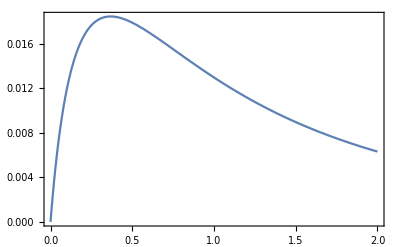
-Graphics-Nucleon.Ge.u

```mathematica
consit=11;io=4;gegm=1;
Labeled[
fig`calc`nucleon`ge`u=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{0,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Ge.u","Subsection"],{{Top,Left}}
]
```

## ge`d

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u11,12d,13s

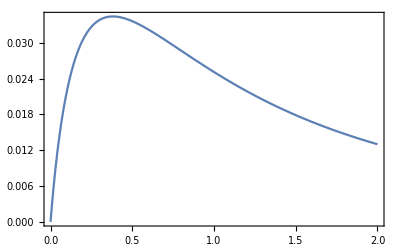
-Graphics-Nucleon.Ge.d

```mathematica
consit=12;io=4;gegm=1;
Labeled[
fig`calc`nucleon`ge`d=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{0,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Ge.d","Subsection"],{{Top,Left}}
]
```

## ge`s

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u,d,13s

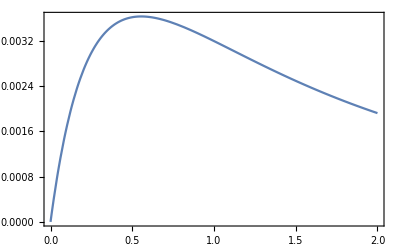
-Graphics-Nucleon.Ge.s

```mathematica
consit=13;io=4;gegm=1;
Labeled[
fig`calc`nucleon`ge`s=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{0,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Ge.s","Subsection"],{{Top,Left}}
]
```

gm

## gm`s`total

```mathematica
consit=4;io=5;gegm=2;
Labeled[
fig`nucleon`ge=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Callout[
rencon⟦consit,io⟧*trgegm⟦consit,io,gegm⟧,
"Tree",
LeaderSize->fig`leadersize
],
Callout[
Piecewise[
{
{rencon⟦consit,io⟧*loopgmd0⟦consit,io⟧,Q2≤fig`cutlimit},
{rencon⟦consit,io⟧*Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
],
"Loop",
LeaderSize->fig`leadersize
],
Callout[
Piecewise[
{
{rencon⟦consit,io⟧*(loopgmd0⟦consit,io⟧+(trgegm⟦consit,io,gegm⟧/.Q2->0)),Q2≤fig`cutlimit},
{rencon⟦consit,io⟧ *(trgegm⟦consit,io,gegm⟧+Re[nugegm⟦consit,io,gegm⟧]),Q2>fig`cutlimit}
}
],
"Total",
LeaderSize->fig`leadersize
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Automatic},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Gm.total","Subsection"],{{Top,Left}}
]
```

-Graphics-Nucleon.Gm.total

## gm`u

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u10,d,13s

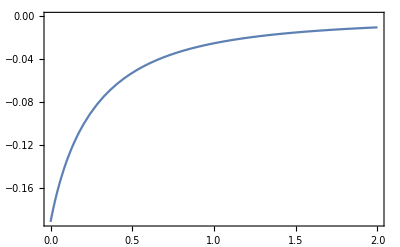
-Graphics-Nucleon.Gm.u

```mathematica
consit=11;io=4;gegm=2;
Labeled[
fig`calc`nucleon`gm`u=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{(*rencon⟦consit,io⟧**)loopgmd0⟦consit,io⟧,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Full},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Gm.u","Subsection"],{{Top,Left}}
]
```

## gm`d

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u11,12d,13s

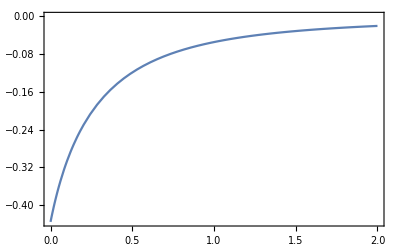
-Graphics-Nucleon.Gm.d

```mathematica
consit=12;io=4;gegm=2;
Labeled[
fig`calc`nucleon`gm`d=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{(*rencon⟦consit,io⟧**)loopgmd0⟦consit,io⟧,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Full},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Gm.d","Subsection"],{{Top,Left}}
]
```

## gm`s

Total, u,d,4s,quench:u, d, 7s,valence:u,d,10s,sea:u,d,13s

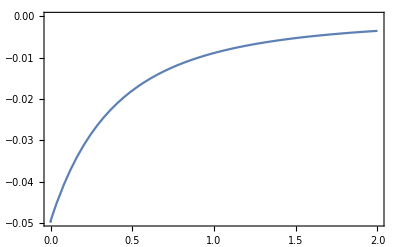
-Graphics-Nucleon.Gm.s

```mathematica
consit=13;io=4;gegm=2;
Labeled[
fig`calc`nucleon`gm`s=Plot[
{
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
Piecewise[
{
{(*rencon⟦consit,io⟧**)loopgmd0⟦consit,io⟧,Q2≤fig`cutlimit},
{(*rencon⟦consit,io⟧**)Re[nugegm⟦consit,io,gegm⟧],Q2>fig`cutlimit}
}
]
},
{Q2,0,2},
AxesOrigin->{0,0},
PlotRange->{{0,2},Full},
PlotRangePadding->{Automatic,Scaled[0.09]},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
],
Style["Nucleon.Gm.s","Subsection"],{{Top,Left}}
]
```

storage

```mathematica
directory`fig="C:\\Users\\Tom\\Desktop\\octet.fig";
```

```mathematica
FileNameJoin[{directory`fig,"fig.calc.nucleon.ge.u.L-1.00"}]
```

C:\Users\Tom\Desktop\octet.fig\fig.calc.nucleon.ge.u.L-1.00

## ge

```mathematica
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.u.L-1.00.m"}],fig`calc`nucleon`ge`u];
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.d.L-1.00.m"}],fig`calc`nucleon`ge`d];
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.s.L-1.00.m"}],fig`calc`nucleon`ge`s];
```

## gm

```mathematica
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.u.L-1.00.m"}],fig`calc`nucleon`gm`u];
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.d.L-1.00.m"}],fig`calc`nucleon`gm`d];
Export[FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.s.L-1.00.m"}],fig`calc`nucleon`gm`s];
```